```mathematica
Clear["Global`*"]
```

```mathematica
inputData = Import[NotebookDirectory[]<>"/input.txt"];
input = StringSplit[inputData];
l=Length[input];(*l will have to be even*)
(*Write a function here that will take in strings as variable names*)
dt=input[[2]];
tmax=input[[4]];
nTrajectory=input[[6]];
nstore=input[[8]];
yWall=input[[10]];
sigmaXX=input[[12]];
sigmaXZ=input[[14]];
transitTime=input[[16]];
sigmaPX=input[[18]];
sigmaPY=input[[20]];
sigmaPZ=input[[22]];
density=input[[24]];
rabi=input[[26]];
kappa=input[[28]];
name =input[[30]]
```

tau1_dens50_g1.4_k20

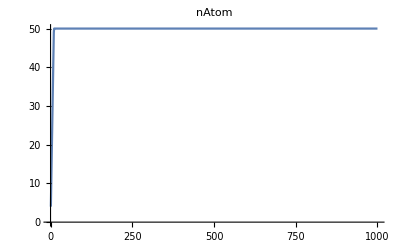

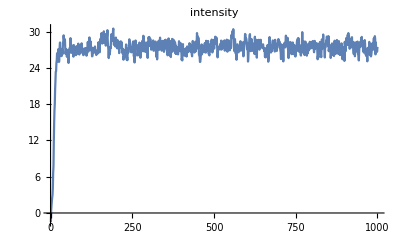

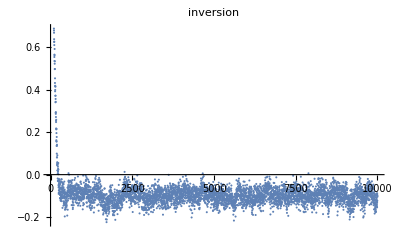

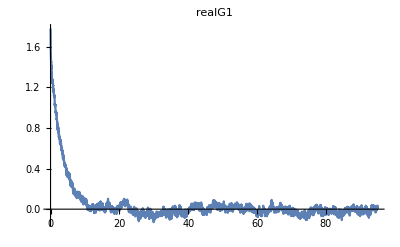

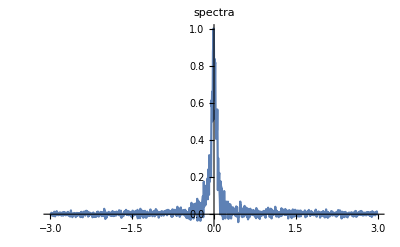

```mathematica
(*When doing one run*)
intensity=Flatten[Import[NotebookDirectory[]<>name<>"/intensity.dat"]];
nAtom=Flatten[Import[NotebookDirectory[]<>name<>"/nAtom.dat"]];
inversionAve=Flatten[Import[NotebookDirectory[]<>name<>"/inversionAve.dat"]];
szFinal=Flatten[Import[NotebookDirectory[]<>name<>"/szFinal.dat"]];
realG1 = Import[NotebookDirectory[]<>name<>"/realG1.dat"];
spectra=Import[NotebookDirectory[]<>name<>"/spectra.dat"];
ListLinePlot[nAtom,PlotRange->All,PlotLabel->"nAtom"]
ListLinePlot[intensity,PlotRange->All,PlotLabel->"intensity"]
ListPlot[szFinal,PlotRange->All,PlotLabel->"inversion"]
ListLinePlot[realG1,PlotRange->All,PlotLabel->"realG1"]
ListLinePlot[spectra,PlotRange->All,PlotLabel->"spectra"]
```

FittedModel[0.00200468/(0.00228222+x^2)]

| Estimate | Standard Error | t-Statistic | P-Value
linewidth | 0.0955452 | 0.00141948 | 67.3099 | 4.35309398662×10^-399
A | 0.041963 | 0.000440831 | 95.1906 | 2.94468760773×10^-544

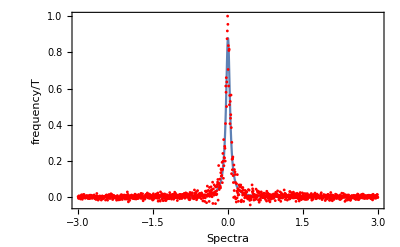

```mathematica
(*Fit the spectra to lorentzian*)
lorentzianModel=A(1/2 linewidth)/(x^2+(1/2 linewidth)^2);
fitLoren=NonlinearModelFit[spectra,{lorentzianModel},{linewidth,A},{x}]
fitLoren["ParameterTable"]
Show[{Plot[fitLoren[x],{x,-3,3},PlotRange->All,BaseStyle->{FontSize->30}],Graphics[{Red,PointSize[.005],Map[Point,spectra]}]},Frame->True,FrameLabel->{"Spectra","frequency/T"}]
```

B ⅇ^(-2 linewidth2 π t)

FittedModel[1.53709 ⅇ^(-0.303768 t)]

| Estimate | Standard Error | t-Statistic | P-Value
linewidth2 | 0.0483461 | 0.000172211 | 280.738 | 6.0948145655×10^-4602
B | 1.53709 | 0.00386566 | 397.626 | 1.4140222279×10^-5923

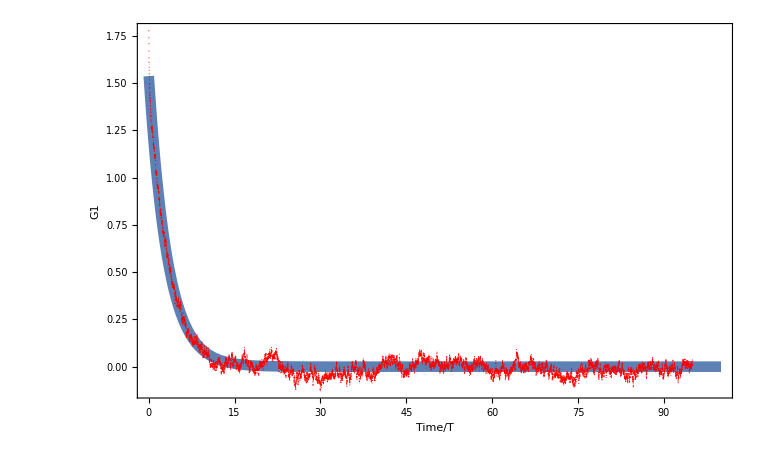

```mathematica
(*Fit the G1 function to exponential*)
exponentialModel=B Exp[-linewidth2*Pi t]
fitExp=NonlinearModelFit[realG1,{exponentialModel},{linewidth2,B},{t}]
fitExp["ParameterTable"]
Show[{Plot[fitExp[x],{x,0,100},PlotRange->All,PlotStyle->{Thickness[0.01]},BaseStyle->{FontSize->30}],Graphics[{Red,PointSize[.001],Map[Point,realG1]}]},Frame->True,FrameLabel->{"Time/T","G1"}]
```

```mathematica
(*Notice there is another exponential decay.*)
```

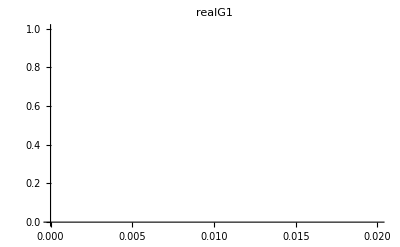

```mathematica
ListPlot[realG1,PlotRange->{{0,0.02},{0,1}}, 
PlotLabel->"realG1"]
```

```mathematica
secondExp=Take[realG1,40];
```

B2 ⅇ^(-2 d π t)

FittedModel[1.6641 ⅇ^(-0.678605 t)]

| Estimate | Standard Error | t-Statistic | P-Value
d | 0.108003 | 0.00563683 | 19.1603 | 3.9933×10^-21
B2 | 1.6641 | 0.0124275 | 133.905 | 1.94905×10^-52

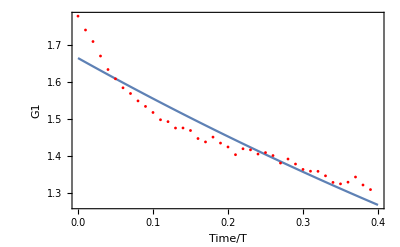

```mathematica
exponentialModel2=B2 Exp[-d*2Pi t]
fitExp2=NonlinearModelFit[secondExp,{exponentialModel2},{d,B2},{t}]
fitExp2["ParameterTable"]
Show[{Plot[fitExp2[x],{x,0,0.4},PlotRange->All,BaseStyle->{FontSize->30}],Graphics[{Red,PointSize[.005],Map[Point,secondExp]}]},Frame->True,FrameLabel->{"Time/T","G1"}]
```